```mathematica
f[x_]=26 x^3 -57 x^2-41 x+102;
```

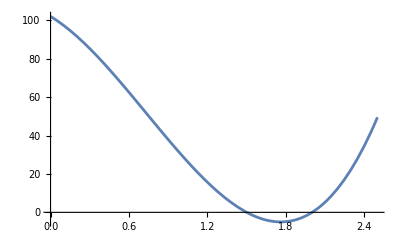

```mathematica
Plot[f[x],{x,0,2.5},AxesOrigin->{0,0,ImageSize->Small}]
```

```mathematica
a=1.8;b=2.5;
If[f[a]*f''[a]>0,
x0=b;g[x_]:=a-f[a]/(f[x]-f[a])*(x-a);
hord[x_,xn_]:=f[xn]+(x-xn)/(xn-a)*(f[xn]-f[a]),
x0=a;g[x_]:=x-f[x]/(f[b]-f[x])*(b-x);
hord[x_,xn_]:=f[xn]+(x-xn)/(xn-b)*(f[xn]-f[b])];
epsil=10^(-3);
```

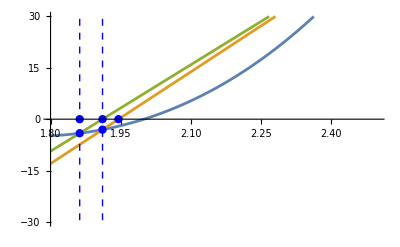

```mathematica
ex=epsil*10;xn1=g[x0];n=1;
While[ex>epsil,
If[n==2,
Print[Plot[{f[x],hord[x,xn1],hord[x,x0],hord[xn01]},{x,a,b},Epilog->{Blue,Dashed,InfiniteLine[{xn1,0},{0,1}],InfiniteLine[{x0,0},{0,1}],PointSize[0.015],Point[{{x0,0},{x0,f[x0]},{xn1,0},{xn1,f[xn1]},{g[xn1],0}}]},PlotRange->30]]];
xn01=x0;x0=xn1;
xn1=g[x0];
ex=(xn1-x0)^2/Abs[xn1+xn01-2*x0];
n=n+1];
```

```mathematica
Print["решение: ",xn1," Найдено на шаге: ",n]
```

решение: 1.99936 Найдено на шаге: 11